#### Two factor production with triangle density that is greater zero everywhere: numerical example 1

```mathematica
c[q_,t_]=a*t*q+q^2/t-g*t;
cq[q_,t_]=a t+2q/t;
ct[q_,t_]=a q-q^2/t^2-g;
cqt[q_,t_]=a-2q/t^2;
cqqt[q_,t_]=-2/t^2;
cqtt[q_,t_]=4q/t^3;
tl=1/4; (*theta lower bar*)
tu=3/4;   (*theta upper bar*)
delta=tu-tl;
(*Assign some parameter values for a,b and g*)
b=16/10;(*principal's utility is bq *)
a=1;
g=1/3;
s[t_]=a t^2/2;
```

```mathematica
f[t_]=(2*9/10*(t-tl))/(delta^2)+1/(10*delta); (*density of theta*)
F[t_]=9/10(t-tl)^2/(delta^2)+(t-tl)/(10*delta);(*distribution*)
```

```mathematica
(*relaxed decision and optimal decision as function of eta*)
Assuming[tu≥t≥tl,Reduce[(b -cq[q,t])f[t]+(1-F[t]) cqt[q,t]==0,q,Reals]]
Assuming[tu≥t≥tl&&n≥0,Reduce[(b -cq[q,t])f[t]+(1-F[t]-n) cqt[q,t]==0,q,Reals]]
```

(t<0||t>0)&&q==(-347 t^2+2944 t^3-2160 t^4)/(330+1440 t^2)

(t==2/9&&n==361/360)||(t==4/5&&n==3129/1000)||(((t<0&&(n<1/40 (33+144 t^2)||n>1/40 (33+144 t^2)))||(t>0&&(n<1/40 (33+144 t^2)||n>1/40 (33+144 t^2))))&&q==(-347 t^2-200 n t^2+2944 t^3-2160 t^4)/(330-400 n+1440 t^2))

```mathematica
(*Straightforward calculation gives the first best and relaxed decision:*)
```

```mathematica
qfb[t_]=-1/2 t (-b+a t);
qr[t_]=(-347 t^2+2944 t^3-2160 t^4)/(330+1440 t^2);
pirt[t_]=-ct[qr[t],t];
pir[t_]= ∫_tl^t pirt[s]ⅆs;
Phir[t_,h_]=pir[t]-pir[h]-c[qr[h],h]+c[qr[h],t];
```

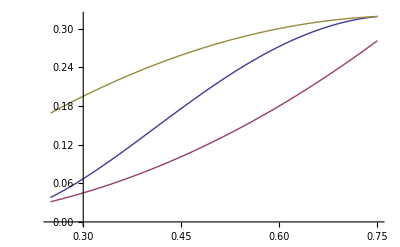

```mathematica
Plot[{qr[t],s[t],qfb[t]},{t,tl,tu}]
```

```mathematica
(*Here I check the sufficient condition in proposition 1. To do so, the mirror images q^v and q^s have to be computed. The results are stored as functions qs1 and qv1. The following Reduce command below verifies that qs1≤qv1 as the opposite statement is "False" in the relevant range. The following plot shows that the first best and the relaxed decision are above s(theta) and both are strictly monotonically increasing. Hence, assumption 1 is also satisfied.*)
VV[q_,t_]=(b q-c[q,t])f[t]+(1-F[t])ct[q,t];
Reduce[{ct[q,t]==ct[qs,t],qs>s[t],tl≤t≤tu,0≤q<s[t]},qs,Reals]
Reduce[{VV[qv,t]==VV[q,t],qv>s[t],0≤q<s[t],tl≤t≤tu},qv,Reals]
```

1/4≤t≤3/4&&0≤q<t^2/2&&qs==-q+t^2

1/4≤t≤3/4&&0≤q<t^2/2&&qv==(-165 q-347 t^2-720 q t^2+2944 t^3-2160 t^4)/(165+720 t^2)

```mathematica
qs1[q_,t_]=t^2-q;
qv1[q_,t_]=(-165 q-347 t^2-720 q t^2+2944 t^3-2160 t^4)/(165+720 t^2);
Reduce[{qs1[q,t]>qv1[q,t],0≤q<s[t],tl≤t≤tu},{q,t},Reals]
```

False

```mathematica
(*The following plot illustrates for which types the non-local incentive constraint is violated
under the relaxed solution*)
```

```mathematica
Plot3D[{Phir[t,h],0},{t,tl,tu},{h,tl,tu}]
```

-Graphics3D-

Now take the parameter values above and use the algorithm. First step is to get for a given eta (i.e. "n") the corresponding decisions, profits and incentive constraints.

```mathematica
qn[t_,n_]=(-347 t^2-200 n t^2+2944 t^3-2160 t^4)/(330-400 n+1440 t^2);
pin[t_,n_]=Assuming[{tl≤t≤tu,0≤n≤1},∫_tl^t -(qn[s,n]-(qn[s,n])^2/(s^2)-1/3)ⅆs];
Phin[t_,h_,n_]=pin[t,n]-pin[h,n]-(h*qn[h,n]+qn[h,n]^2/h-1/3 h)+(t*qn[h,n]+qn[h,n]^2/t-1/3 t);
```

```mathematica
NMinimize[{Phin[t,h,n]/.{n->0},1/4≤h≤t≤3/4},{{t,7/10,3/4},{h,1/4,3/10}}]
```

{-0.00989799,{h→0.25,t→0.75}}

Next, Phin is minimized and the minimizers as well as the minimum value is reported :

```mathematica
For[i=1,i<11,i++,Print[N[5*i/100,6]];Print[NMinimize[{Phin[t,h,n]/.{n->5*i/100},1/4≤h≤t≤3/4},{{t,7/10,3/4},{h,1/4,3/10}}]]]
```

0.05

{-0.0092601,{h→0.25,t→0.75}}

0.1

{-0.00855892,{h→0.25,t→0.75}}

0.15

{-0.00778519,{h→0.25,t→0.75}}

0.2

{-0.0069278,{h→0.25,t→0.75}}

0.25

{-0.00597332,{h→0.25,t→0.75}}

0.3

{-0.00490529,{h→0.25,t→0.75}}

0.35

{-0.00370337,{h→0.25,t→0.75}}

0.4

{-0.00234208,{h→0.25,t→0.75}}

0.45

{-0.000789137,{h→0.25,t→0.75}}

0.5

{0.000997187,{h→0.25,t→0.75}}

```mathematica
(*The relevant \bar{eta} turns out to be around 0.47:*)
```

```mathematica
For[i=472980,i<472985,i++,Print[N[i/1000000,6]];Print[NMinimize[{Phin[t,h,n]/.{n->i/1000000},1/4≤h≤t≤3/4},{{t,7/10,3/4},{h,1/4,3/10}}]]]
```

0.47298

{-7.5916×10^-8,{t→0.75,h→0.25}}

0.472981

{-4.04419×10^-8,{t→0.75,h→0.25}}

0.472982

{-4.96768×10^-9,{t→0.75,h→0.25}}

0.472983

{3.05066×10^-8,{t→0.75,h→0.25}}

0.472984

{6.59811×10^-8,{t→0.75,h→0.25}}

```mathematica
(*Ok, eta bar would be 0.472982. The constraint is only binding from top to bottom and not at any interior types.*)
```

```mathematica
(*Now, the solution denoted by qs. Obviously, all t have the same eta, i.e. eta=0.472982*
```

```mathematica
qs[t_]=qn[t,47298/100000]
```

(-(110399 t^2)/250+2944 t^3-2160 t^4)/(17601/125+1440 t^2)

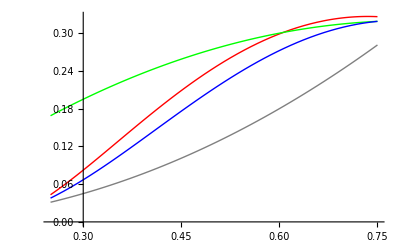

```mathematica
Plot[{qs[t],s[t],qfb[t],qr[t]},{t,tl,tu},PlotStyle->{Red,Gray,Green,Blue}]
```

```mathematica
(*Plotting the rent as functon of type*)
```

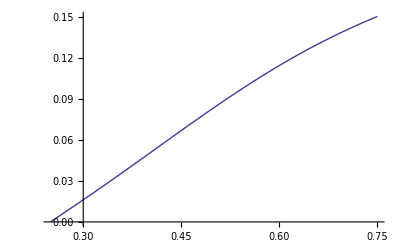

```mathematica
Plot[pin[t,472982/1000000],{t,1/4,3/4}]
```

```mathematica
FullSimplify[{qs[t],s[t],qfb[t],qr[t],qn[t,n]}]
```

{(t^2 (-110399+4000 (184-135 t) t))/(6 (5867+60000 t^2)),t^2/2,-1/2 (-8/5+t) t,(t^2 (-347+16 (184-135 t) t))/(30 (11+48 t^2)),(t^2 (347+200 n+16 t (-184+135 t)))/(10 (-33+40 n-144 t^2))}